```mathematica
Full Simplif
```

```mathematica
j0[x_]:=Sin[x]/x
n0[x_]:=-Cos[x]/x
```

```mathematica
j0'[k a]
j0'[α a]
n0'[k a]
n0'[α a]
j0'[B]
j0'[A]
n0'[B]
n0'[A]
```

Cos[a k]/(a k)-Sin[a k]/(a^2 k^2)

Cos[a α]/(a α)-Sin[a α]/(a^2 α^2)

Cos[a k]/(a^2 k^2)+Sin[a k]/(a k)

Cos[a α]/(a^2 α^2)+Sin[a α]/(a α)

Cos[B]/B-Sin[B]/B^2

Cos[A]/A-Sin[A]/A^2

Cos[B]/B^2+Sin[B]/B

Cos[A]/A^2+Sin[A]/A

```mathematica
Clear[j0,n0]
```

```mathematica
Clear[j0,n0]
((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B])/.{A->α a,B->k a}
((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B])
Simplify[((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B]),Assumptions->α∈Reals&&α>0&&a∈Reals&&a>0&&k∈Reals&&k>0]/.{A->α a,B->k a}
Simplify[((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B]),Assumptions->α∈Reals&&α>0&&a∈Reals&&a>0&&k∈Reals&&k>0]
j0[x_]:=Sin[x]/x
n0[x_]:=-Cos[x]/x
((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B])/.{A->α a,B->k a}
((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B])
Simplify[((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B]),Assumptions->α∈Reals&&α>0&&a∈Reals&&a>0&&k∈Reals&&k>0]/.{A->α a,B->k a}
Simplify[((B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B])/((B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B]),Assumptions->α∈Reals&&α>0&&a∈Reals&&a>0&&k∈Reals&&k>0]
```

(k j0[a α] j0'[a k]-α j0[a k] j0'[a α])/(-α n0[a k] j0'[a α]+k j0[a α] n0'[a k])

(-(A j0[B] j0'[A])/a+(B j0[A] j0'[B])/a)/(-(A n0[B] j0'[A])/a+(B j0[A] n0'[B])/a)

(-a k j0[a α] j0'[a k]+a α j0[a k] j0'[a α])/(a α n0[a k] j0'[a α]-a k j0[a α] n0'[a k])

(A j0[B] j0'[A]-B j0[A] j0'[B])/(A n0[B] j0'[A]-B j0[A] n0'[B])

((k (Cos[a k]/(a k)-Sin[a k]/(a^2 k^2)) Sin[a α])/(a α)-(α Sin[a k] (Cos[a α]/(a α)-Sin[a α]/(a^2 α^2)))/(a k))/((k (Cos[a k]/(a^2 k^2)+Sin[a k]/(a k)) Sin[a α])/(a α)+(α Cos[a k] (Cos[a α]/(a α)-Sin[a α]/(a^2 α^2)))/(a k))

(-(A (Cos[A]/A-Sin[A]/A^2) Sin[B])/(a B)+(B Sin[A] (Cos[B]/B-Sin[B]/B^2))/(a A))/((A Cos[B] (Cos[A]/A-Sin[A]/A^2))/(a B)+(B Sin[A] (Cos[B]/B^2+Sin[B]/B))/(a A))

(-a α Cos[a α] Sin[a k]+a k Cos[a k] Sin[a α])/(a α Cos[a k] Cos[a α]+a k Sin[a k] Sin[a α])

(B Cos[B] Sin[A]-A Cos[A] Sin[B])/(A Cos[A] Cos[B]+B Sin[A] Sin[B])

```mathematica
(B/a) j0[A]j0'[B]-(A/a) j0'[A]j0[B]
(B/a) j0[A]n0'[B]-(A/a)j0'[A]n0[B]
```

-(A (Cos[A]/A-Sin[A]/A^2) Sin[B])/(a B)+(B Sin[A] (Cos[B]/B-Sin[B]/B^2))/(a A)

(A Cos[B] (Cos[A]/A-Sin[A]/A^2))/(a B)+(B Sin[A] (Cos[B]/B^2+Sin[B]/B))/(a A)

```mathematica
(c-d-b Sin[a]Sin[b]+a Sin[a] Sin[b])/(e+f-a Sin[a] Cos[b]+b Sin[a]Cos[b])
```

(c-d+a Sin[a] Sin[b]-b Sin[a] Sin[b])/(e+f-a Cos[b] Sin[a]+b Cos[b] Sin[a])

```mathematica
FullSimplify[ExpToTrig[TrigToExp[Expand[FullSimplify[(c-d-b Sin[a]Sin[b]+a Sin[a] Sin[b])/(e+f-a Sin[a] Cos[b]+b Sin[a]Cos[b]),Assumptions->c∈Reals&&c>0&&d∈Reals&&d>0&&a∈Reals&&a>0&&b∈Reals&&b>0&&e∈Reals&&e>0&&f∈Reals&&f>0]]]]]
```

(c-d+(a-b) Sin[a] Sin[b])/(e+f+(-a+b) Cos[b] Sin[a])

```mathematica
Sin[x]/Cos[y]
```

Sec[y] Sin[x]

```mathematica
/
```

```mathematica
Tan[b]Cot[b]
```

1

```mathematica
(B-A Tan[B]Cot[A])/(B Tan[B]-A Tan[A])
```

(B-A Cot[A] Tan[B])/(-A Tan[A]+B Tan[B])

```mathematica
G(A+B)/(c+d)
```

((A+B) G)/(c+d)

```mathematica
FullSimplify[(B Tan[A]-A Tan[B])/(B Tan[B]Tan[A]+1),Assumptions->A∈Reals&&A>0&&B∈Reals&&B>0]
```

(B Tan[A]-A Tan[B])/(1+B Tan[A] Tan[B])

```mathematica
FullSimplify[( Tan[A]- Tan[B])/(Tan[B]Tan[A]+1),Assumptions->A∈Reals&&A>0&&B∈Reals&&B>0]
```

```mathematica
Tan[A-B]/.{A->α a,B->k a}
```

-Tan[a k-a α]

```mathematica
D[((k/alpha)Tan[alpha a]-Tan[k a])/((k/alpha)Tan[k a]Tan[a alpha]+1),k]
```

-(((k Tan[a alpha])/alpha-Tan[a k]) ((a k Sec[a k]^2 Tan[a alpha])/alpha+(Tan[a alpha] Tan[a k])/alpha))/(1+(k Tan[a alpha] Tan[a k])/alpha)^2+(-a Sec[a k]^2+Tan[a alpha]/alpha)/(1+(k Tan[a alpha] Tan[a k])/alpha)

```mathematica
FullSimplify[((k/alpha)Tan[alpha a]-Tan[k a])/((k/alpha)Tan[k a]Tan[a alpha]+1)]
```

(k Tan[a alpha]-alpha Tan[a k])/(alpha+k Tan[a alpha] Tan[a k])

```mathematica
-(((-(α Tan[a k])+k Tan[a α]) (a k Sec[a k]^2 Tan[a α]+Tan[a k] Tan[a α]))/(α+k Tan[a k] Tan[a α])^2)+(-(a α Sec[a k]^2)+Tan[a α])/(α+k Tan[a k] Tan[a α])
```

-((-α Tan[a k]+k Tan[a α]) (a k Sec[a k]^2 Tan[a α]+Tan[a k] Tan[a α]))/(α+k Tan[a k] Tan[a α])^2+(-a α Sec[a k]^2+Tan[a α])/(α+k Tan[a k] Tan[a α])

```mathematica
(a-Tan[λ a]/λ/.λ->Sqrt[2m V0/ℏ^2])^2
```

(a-Tan[√2 a √((m V0)/ℏ^2)]/(√2 √((m V0)/ℏ^2)))^2

```mathematica
TableForm[Simplify[Table[D[(a-Tan[λ a]/λ/.λ->Sqrt[2m V0/ℏ^2])^2,{a,y}],{y,0,6}]]]
%/.a->0
%
```

(a-Tan[√2 a √((m V0)/ℏ^2)]/(√2 √((m V0)/ℏ^2)))^2
-2 Tan[√2 a √((m V0)/ℏ^2)]^2 (a-Tan[√2 a √((m V0)/ℏ^2)]/(√2 √((m V0)/ℏ^2)))
-1/2 Sec[√2 a √((m V0)/ℏ^2)]^3 (8 √2 a √((m V0)/ℏ^2) Cos[√2 a √((m V0)/ℏ^2)]-11 Sin[√2 a √((m V0)/ℏ^2)]+Sin[3 √2 a √((m V0)/ℏ^2)]) Tan[√2 a √((m V0)/ℏ^2)]
-√((m V0)/ℏ^2) Sec[√2 a √((m V0)/ℏ^2)]^5 (12 a √((m V0)/ℏ^2) Cos[√2 a √((m V0)/ℏ^2)]-4 a √((m V0)/ℏ^2) Cos[3 √2 a √((m V0)/ℏ^2)]+√2 (-19 Sin[√2 a √((m V0)/ℏ^2)]+5 Sin[3 √2 a √((m V0)/ℏ^2)]))
(8 m V0 Sec[√2 a √((m V0)/ℏ^2)]^5 (-9 √2 a √((m V0)/ℏ^2) Cos[√2 a √((m V0)/ℏ^2)]+√2 a √((m V0)/ℏ^2) Cos[3 √2 a √((m V0)/ℏ^2)]+27 Sin[√2 a √((m V0)/ℏ^2)]-3 Sin[3 √2 a √((m V0)/ℏ^2)]) Tan[√2 a √((m V0)/ℏ^2)])/ℏ^2
2 ((m V0)/ℏ^2)^(3/2) Sec[√2 a √((m V0)/ℏ^2)]^7 (-160 a √((m V0)/ℏ^2) Cos[√2 a √((m V0)/ℏ^2)]+100 a √((m V0)/ℏ^2) Cos[3 √2 a √((m V0)/ℏ^2)]-4 a √((m V0)/ℏ^2) Cos[5 √2 a √((m V0)/ℏ^2)]+554 √2 Sin[√2 a √((m V0)/ℏ^2)]-159 √2 Sin[3 √2 a √((m V0)/ℏ^2)]+7 √2 Sin[5 √2 a √((m V0)/ℏ^2)])
-(8 m^2 V0^2 Sec[√2 a √((m V0)/ℏ^2)]^8 (-1088+1236 Cos[2 √2 a √((m V0)/ℏ^2)]-192 Cos[4 √2 a √((m V0)/ℏ^2)]+4 Cos[6 √2 a √((m V0)/ℏ^2)]+245 √2 a √((m V0)/ℏ^2) Sin[2 √2 a √((m V0)/ℏ^2)]-56 √2 a √((m V0)/ℏ^2) Sin[4 √2 a √((m V0)/ℏ^2)]+√2 a √((m V0)/ℏ^2) Sin[6 √2 a √((m V0)/ℏ^2)]))/ℏ^4

{0,0,0,0,0,0,(320 m^2 V0^2)/ℏ^4}

{0,0,0,0,0,0,(320 m^2 V0^2)/ℏ^4}

```mathematica
TableForm[Simplify[Table[D[(a-Tan[λ a]/λ)^2,{a,y}],{y,0,6}]]]
%/.a->0
%/.λ->Sqrt[2m V0/ℏ^2]
```

(a-Tan[a λ]/λ)^2
(2 Tan[a λ]^2 (-a λ+Tan[a λ]))/λ
-1/2 Sec[a λ]^3 (8 a λ Cos[a λ]-11 Sin[a λ]+Sin[3 a λ]) Tan[a λ]
λ Sec[a λ]^5 (-6 a λ Cos[a λ]+2 a λ Cos[3 a λ]+19 Sin[a λ]-5 Sin[3 a λ])
4 λ^2 Sec[a λ]^5 (-9 a λ Cos[a λ]+a λ Cos[3 a λ]+27 Sin[a λ]-3 Sin[3 a λ]) Tan[a λ]
-λ^3 Sec[a λ]^7 (80 a λ Cos[a λ]-50 a λ Cos[3 a λ]+2 a λ Cos[5 a λ]-554 Sin[a λ]+159 Sin[3 a λ]-7 Sin[5 a λ])
-2 λ^4 Sec[a λ]^8 (-1088+1236 Cos[2 a λ]-192 Cos[4 a λ]+4 Cos[6 a λ]+245 a λ Sin[2 a λ]-56 a λ Sin[4 a λ]+a λ Sin[6 a λ])

{0,0,0,0,0,0,80 λ^4}

{0,0,0,0,0,0,(320 m^2 V0^2)/ℏ^4}

```mathematica
D[(a-Tan[λ a]/λ/.λ->Sqrt[2m V0/ℏ^2])^2,{a,6}]/.a->0
```

(320 m^2 V0^2)/ℏ^4

```mathematica
4π Normal[Series[(a-Tan[λ a]/λ/.λ->Sqrt[2m V0/ℏ^2])^2,{a,0,6}]]
```

(16 a^6 m^2 π V0^2)/(9 ℏ^4)

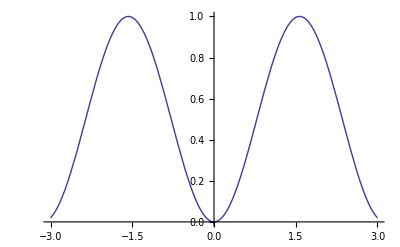

```mathematica
Plot[Sin[x]^2,{x,-3,3}]
```

```mathematica
s
```

```mathematica
Tan[3π/2]
```

ComplexInfinity

```mathematica
Solve[Tan[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Tan[x]==x,x]

```mathematica
1/Csc[-d]^2
```

Sin[d]^2

```mathematica
Csc[d]
```

Csc[d]

```mathematica
FullSimplify[Normal[Series[-2 Cot[-k a]/k-1/a,{k,0,1}]]]
```

(-3-2 a^2+6/k^2)/(3 a)

```mathematica
Normal[Series[Cot[-k a],{k,0,1}]]
```

-1/(a k)+(a k)/3

```mathematica
Solve[k Normal[Series[Cot[-k a],{k,0,1}]]==-1/a-1/2 γeff k^2,γeff]
```

{{γeff→-(2 a)/3}}

```mathematica
FullSimplify[Solve[Normal[Series[4π/((1/L+(1/2)γeff k^2)^2+k^2)==4π/k^2  Sin[k a]^2,γeff],Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&L∈Reals&&L>0]
```

{{γeff→(2 (-1+k L Cot[a k]))/(k^2 L)},{γeff→-(2 (1+k L Cot[a k]))/(k^2 L)}}

```mathematica
4π/((1/L+(1/2)γeff k^2)^2+k^2)
```

(4 π)/(k^2+(1/L+(k^2 γeff)/2)^2)

```mathematica
FullSimplify[Solve[Normal[Series[4π/((1/L+(1/2)γeff k^2)^2+k^2),{k,0,2}]]==Normal[Series[4π/k^2  Sin[k a]^2,{k,0,0}]],γeff],Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&L∈Reals&&L>0]
```

{{γeff→-(a^2-L^2+k^2 L^4)/(k^2 L^3)}}

```mathematica
FullSimplify[Solve[Normal[Series[4π/((1/L+(1/2)γeff k^2)^2+k^2),{k,0,2}]]==4π/k^2 Normal[Series[ Sin[k a]^2,{k,0,1}]],γeff],Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&L∈Reals&&L>0]
```

{{γeff→1/(k^2 L)-L}}

```mathematica
Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&L∈Reals&&L>0
```

```mathematica
FullSimplify[Solve[4π/((1/L+(1/2)γeff k^2)^2+k^2)==4π/k^2  Sin[k a]^2,γeff],Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&L∈Reals&&L>0]
```

{{γeff→(2 (-1+k L Cot[a k]))/(k^2 L)},{γeff→-(2 (1+k L Cot[a k]))/(k^2 L)}}

```mathematica
FullSimplify[(2 (-1+k L Normal[Series[ Cot[a k],{k,0,0}]]))/(k^2 L)]
```

(2 (-1+L/a))/(k^2 L)

```mathematica
Normal[Series[(4 π)/(k^2+(1/L+(k^2 γeff)/2)^2),{k,0,2}]]
```

4 L^2 π+k^2 (-4 L^4 π-4 L^3 π γeff)

```mathematica
Normal[Series[(4π /k^2)Sin[k a]^2,{k,0,1}]]
```

4 a^2 π

```mathematica
Solve[4 L^2 π+k^2 (-4 L^4 π-4 L^3 π γeff)==4 a^2 π,γeff]
```

{{γeff→(-a^2+L^2-k^2 L^4)/(k^2 L^3)}}

```mathematica
Sqrt[0]
```

0

```mathematica
Limit[Tan[Sqrt[b x]a ]/Sqrt[b x],x->-∞]
```

Limit[Tan[a √(b x)]/(√(b x)),x→-∞]

```mathematica
0/0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[x/x,x->0]
```

1

```mathematica
Tan[∞]
```

Interval[{-∞,∞}]

```mathematica
FullSimplify[A^2(Cos[A]/(Sin[A]A)-1/A)]
```

A (-1+Cot[A])

```mathematica
A^2(
```

```mathematica
Cot[A]Tan[A]
```

1

```mathematica
Limit[ArcTan[x],x->-∞]
```

-π/2

```mathematica
Limit[Tan[Sqrt[x]],x->-∞]
```

ⅈ

```mathematica
Limit[ArcTan[1/Tan[Sqrt[x]],x->-∞]
```

```mathematica
Limit[-k + ArcTan[1/(1+2 V0) Tan[Sqrt[1+2 V0]]],V0->∞,Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&m∈Reals&&m>0]
Limit[-k a + ArcTan[k/(k^2+2m V0/ℏ^2) Tan[Sqrt[k+2m/ℏ^2 V0]a]],V0->∞,Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&m∈Reals&&m>0]
```

$Aborted

$Aborted

```mathematica
Limit[-k + ArcTan[1/(1+2 V0) Tan[Sqrt[1+2 V0]]],V0->∞,Assumptions->k∈Reals&&k>0&&a∈Reals&&a>0&&m∈Reals&&m>0]
```

$Aborted

```mathematica
Limit[k/Sqrt[k^2+2m/ℏ^2V0],V0->-∞]
```

0

```mathematica
Limit[k/Sqrt[k^2+2m/ℏ^2V0],V0->-∞]
```

0

```mathematica
Limit[Tan[Sqrt[V0]],V0->-∞]
```

ⅈ

```mathematica
Limit[ArcTan[1/Sqrt[x]  Tan[x]],{x->-∞}]
```

{Limit[ArcTan[Tan[x]/(√x)],x→-∞]}

```mathematica
0ⅈ
```

0

```mathematica
ArcTan[0]
```

0

```mathematica
Limit[Sqrt[x],x->-∞]
```

ⅈ ∞